```mathematica
iuj
```

```mathematica
q
```

```mathematica
jh
```

```mathematica
Reverse[Range[4]]
```

{4,3,2,1}

```mathematica
Reverse[Range[50]]
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
PieChart[Range[50]]
```

-Graphics-

```mathematica
NumberLinePlot[Range[5]^2]
```

-Graphics-

```mathematica
IntegerDigits[198798]
```

{1,9,8,7,9,8}

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Plot[n^2,{n, -5, 5}]
```

-Graphics-

```mathematica
Table[1000, 5]
```

{1000,1000,1000,1000,1000}

```mathematica
Table[n^3, {n, Range[10,20]}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

```mathematica
Table[x^2-y^2-z^2, {x,5}, {y,5}, {z,5}]
```

{{{-1,-4,-9,-16,-25},{-4,-7,-12,-19,-28},{-9,-12,-17,-24,-33},{-16,-19,-24,-31,-40},{-25,-28,-33,-40,-49}},{{2,-1,-6,-13,-22},{-1,-4,-9,-16,-25},{-6,-9,-14,-21,-30},{-13,-16,-21,-28,-37},{-22,-25,-30,-37,-46}},{{7,4,-1,-8,-17},{4,1,-4,-11,-20},{-1,-4,-9,-16,-25},{-8,-11,-16,-23,-32},{-17,-20,-25,-32,-41}},{{14,11,6,-1,-10},{11,8,3,-4,-13},{6,3,-2,-9,-18},{-1,-4,-9,-16,-25},{-10,-13,-18,-25,-34}},{{23,20,15,8,-1},{20,17,12,5,-4},{15,12,7,0,-9},{8,5,0,-7,-16},{-1,-4,-9,-16,-25}}}

```mathematica
Table[n, {n, Range[20]}, 2]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,7},{8,8},{9,9},{10,10},{11,11},{12,12},{13,13},{14,14},{15,15},{16,16},{17,17},{18,18},{19,19},{20,20}}

```mathematica
Range[0,20,2]
```

{0,2,4,6,8,10,12,14,16,18,20}

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
CurrentImage[]
```

-Graphics-

```mathematica
ColorNegate[CurrentImage[]]
```

-Graphics-

```mathematica
EdgeDetect[CurrentImage[]]
```

-Graphics-

```mathematica
EdgeDetect[CurrentImage[]]
```

-Graphics-

```mathematica
Table[2, "hello"]
```

Table::iterb: Iterator {hello} does not have appropriate bounds.

Table[2,{hello}]

```mathematica
Table ["hello",2]
```

{hello,hello}

```mathematica
StringJoin[Table["hello",2]]
```

hellohello

```mathematica
StringJoin[ToUpperCase[Alphabet[]]]
```

ABCDEFGHIJKLMNOPQRSTUVWXYZ

```mathematica
StringJoin[Table["AGCT", 100]]
```

AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT

```mathematica
StringTake[StringJoin[Alphabet[]], 6]
```

abcdef

```mathematica
Rasterize[StringJoin[Alphabet[]]]
```

-Graphics-

```mathematica
BarChart[StringLength[TextWords["A long time ago, in a galaxy far, far away"]]]
```

-Graphics-

```mathematica
StringLength[WikipediaData["computer"]]
```

51697

```mathematica
Length[TextWords[WikipediaData["computer"]]]
```

7984

```mathematica
Take[TextSentences[WikipediaData["strings"]], 1]
```

{String (structure) is a long flexible structure made from threads twisted together, which is used to tie, bind, or hang other objects.}

```mathematica
StringJoin[StringTake[TextSentences[WikipediaData["computers"]],1]]
```

ATSTTSEMTTCTPP="TTFTTT=TLTTTSITIIDMTTAAATTTIAATAIBIATITIITS=CATFTTTAEBNH=HTTTLHTWAB=TDETTITPIRT=TEIBTDTTHACIINCTALOIIIHBTTHTVTE=CWATIHJTIWIAATBAITFCSTATHT=TDTKINHPTWTTC=TIET=TTSCSCCATDIRTPIWJSAITETSHTALATSGETTLSIETWOAMTTRACRIIISFIIGDOHCIAMA=TOBItSTBSITMSTSS=SCCW=TMIALITHTFMPWSTCBOTI=TTSTTITMWITCUTTS=FTHHIT=TAALTP=TBOBSA=TTITTITCIIA"W"A=HFMMH=QCSLTTT=C=T=

```mathematica
Max[StringLength[WordList[]]]
```

23

```mathematica
StringTake[WordList[], 1]
```

{a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,40059,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z}
 |  |  |  |

```mathematica
]
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
ListLinePlot[Take[StringLength[WordList[]], 1000]]
```

-Graphics-

```mathematica
Table[x,4,5]
```

{{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x},{x,x,x,x,x}}

```mathematica
Grid[Table[x,4,5]]
```

x | x | x | x | x
x | x | x | x | x
x | x | x | x | x
x | x | x | x | x

```mathematica
Grid[Table[4, {i,4}, {j,i}]]
```

4 |  |  | 
4 | 4 |  | 
4 | 4 | 4 | 
4 | 4 | 4 | 4

```mathematica
Grid[Table[i*j, {i,12}, {j,12}]]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144

```mathematica
Grid[Table[RomanNumeral[i*j], {i,5}, {j,5}]]
```

I | II | III | IV | V
II | IV | VI | VIII | X
III | VI | IX | XII | XV
IV | VIII | XII | XVI | XX
V | X | XV | XX | XXV

```mathematica
Grid[Table[RandomColor[], {i, 10}, {j,10}]]
```

RGBColor[0.7512332072844334, 0.05770278490186764, 0.5707221694680509] | RGBColor[0.46974448002223945, 0.43480657669827916, 0.8086006193179245] | RGBColor[0.8865690407093103, 0.08996135619547263, 0.7071971349333734] | RGBColor[0.9210997499818621, 0.9574908737273844, 0.24825304968995643] | RGBColor[0.5610150059670096, 0.4360018594215733, 0.20527858740826432] | RGBColor[0.06294439007237829, 0.6741965826514937, 0.07832209843048821] | RGBColor[0.698628592965421, 0.016451797601528595, 0.07894741896249924] | RGBColor[0.9298884955793274, 0.2215403191497023, 0.4970529063509339] | RGBColor[0.672650619266884, 0.8301365610098042, 0.9454327822744262] | RGBColor[0.8157358634855649, 0.8822850967704055, 0.4126219060697336]
RGBColor[0.6589824518110687, 0.569725705427361, 0.1298028546189114] | RGBColor[0.5125503350774732, 0.550681795786494, 0.8253683462240833] | RGBColor[0.9633012121551217, 0.4811101552389656, 0.9325218578382128] | RGBColor[0.6555826164826832, 0.08584615677513696, 0.5017193841052054] | RGBColor[0.3039550480743498, 0.8699055774996334, 0.267899887619391] | RGBColor[0.13760947176345262, 0.49465550379132117, 0.33896806547187275] | RGBColor[0.14111313713932216, 0.531162404788903, 0.3308138059379859] | RGBColor[0.8016581740166788, 0.03812065167713308, 0.0440206417285649] | RGBColor[0.6742793083292493, 0.3289294177243116, 0.04645407552756198] | RGBColor[0.20945751951157554, 0.7159998164582342, 0.4445814287682386]
RGBColor[0.35803632580280276, 0.3638340114106946, 0.6164079038896597] | RGBColor[0.9924138606011068, 0.3129067597341031, 0.6994964641404786] | RGBColor[0.5745455759411091, 0.4816831689800125, 0.3572892688160567] | RGBColor[0.6225487664672178, 0.8200946577615169, 0.5193251519182405] | RGBColor[0.5694116305800028, 0.8361719153242342, 0.29734956966712667] | RGBColor[0.6027776139303385, 0.08819964638243594, 0.9705002493737311] | RGBColor[0.23208137072781443, 0.5642538535328088, 0.5385112712815614] | RGBColor[0.5556591893316813, 0.523043390734838, 0.08696476702470246] | RGBColor[0.06324378051871227, 0.060225853270686525, 0.4289778624483982] | RGBColor[0.6229210936523633, 0.48187089542697215, 0.0030880284189180873]
RGBColor[0.1595090627773541, 0.28806041628096035, 0.7687883608856616] | RGBColor[0.5271163225661035, 0.3712595068087603, 0.6139097199069194] | RGBColor[0.9344731977298026, 0.6767982472836302, 0.9263724590837119] | RGBColor[0.8270456160907538, 0.04196526709662152, 0.2505469345539548] | RGBColor[0.055040332915102574, 0.5681872605082599, 0.2689133728777411] | RGBColor[0.04897157762847959, 0.6989966078415304, 0.11524276096555486] | RGBColor[0.7606176543758154, 0.183839741336719, 0.40816088970912934] | RGBColor[0.13516939095743252, 0.42678383064893644, 0.9820745897382268] | RGBColor[0.04836418159855804, 0.631591549698505, 0.19742858638468608] | RGBColor[0.5099027208244424, 0.26783268206484045, 0.7388295941942922]
RGBColor[0.6257624368081645, 0.6491566015149113, 0.824675222043944] | RGBColor[0.6082622003251388, 0.15992687973046182, 0.6336684117121005] | RGBColor[0.9136473649628924, 0.5491038191236892, 0.10212132592652146] | RGBColor[0.35303089141424193, 0.12658390446734646, 0.10995787455572037] | RGBColor[0.13386628658655608, 0.3234232967684634, 0.14718727996244207] | RGBColor[0.19731292147385826, 0.23176433044668943, 0.9710881019086672] | RGBColor[0.7722265046736208, 0.09509767340378028, 0.617785374863046] | RGBColor[0.50670258155493, 0.336265522443836, 0.14092588237262826] | RGBColor[0.49622801270389827, 0.6944859025197434, 0.11728760031585517] | RGBColor[0.165240487058123, 0.6169614617956862, 0.3411018146083149]
RGBColor[0.6842616590994544, 0.8213865642096336, 0.8010425752009493] | RGBColor[0.07875505523494986, 0.19714022365849493, 0.5406300654653049] | RGBColor[0.10666894552501072, 0.4720738786208676, 0.24778777802563834] | RGBColor[0.769272245490118, 0.3546762252874731, 0.7063630175041484] | RGBColor[0.6336682310605857, 0.3783118214075871, 0.7356835273333397] | RGBColor[0.8804973093930863, 0.6215291755421237, 0.49248585169080816] | RGBColor[0.8716257023118428, 0.40246041931327325, 0.432440170949727] | RGBColor[0.14659817824363697, 0.7138549959700258, 0.9893423161375601] | RGBColor[0.6429783653983372, 0.8203941212237944, 0.8591886468710928] | RGBColor[0.45076787600806356, 0.9646263907433608, 0.6663014084382557]
RGBColor[0.8327803875013913, 0.18820660291707814, 0.9157920592452811] | RGBColor[0.6215549556582705, 0.30233423293773476, 0.24774766766634282] | RGBColor[0.22663508079696149, 0.21585560229876988, 0.40820335013358444] | RGBColor[0.8708187354097876, 0.4463653783457677, 0.9724549167432235] | RGBColor[0.8440206773524819, 0.46854372754724327, 0.846353360478576] | RGBColor[0.9541244524133887, 0.1671430826592879, 0.13559907786773673] | RGBColor[0.35418655279192923, 0.3814760335832825, 0.23433524623795354] | RGBColor[0.054913088408469424, 0.5207769702595149, 0.5129191051142903] | RGBColor[0.2891337843338242, 0.7694857171670311, 0.21387957489170528] | RGBColor[0.30654052092811535, 0.9859948223448878, 0.24237049094846141]
RGBColor[0.27519074656661946, 0.04475357071586106, 0.1728412728671107] | RGBColor[0.4089455110743978, 0.9574259597528889, 0.21479108710137385] | RGBColor[0.9946356205460496, 0.46637127696315384, 0.26082293702722126] | RGBColor[0.8513679488822965, 0.38879811764108485, 0.5504244891302366] | RGBColor[0.8296303574660238, 0.22204592123376954, 0.7749514462634803] | RGBColor[0.36608316732593216, 0.08452046323380613, 0.4812860066893012] | RGBColor[0.5556756096062485, 0.1452605145186836, 0.6715908996988289] | RGBColor[0.25484549594481143, 0.6183341689166579, 0.8931510421734259] | RGBColor[0.31300979594648326, 0.2518657017295529, 0.3651280736461133] | RGBColor[0.18648033716107992, 0.4729070769296697, 0.30593497245263634]
RGBColor[0.6168841441137562, 0.06392198299149743, 0.041079593047869345] | RGBColor[0.9268185531794806, 0.8142465744914109, 0.3402548853615681] | RGBColor[0.15968339569071932, 0.046556394627263575, 0.9791994963123594] | RGBColor[0.5480146608140954, 0.8244916074340083, 0.5390653832481342] | RGBColor[0.383841839242973, 0.2847067383191515, 0.4353078208698551] | RGBColor[0.6693686779779817, 0.7654612243281793, 0.22585893011061198] | RGBColor[0.5563668940961, 0.1940386804120322, 0.2948718033249398] | RGBColor[0.35223258587427697, 0.31616723445643835, 0.642985336823473] | RGBColor[0.6411009550636824, 0.005620620827774037, 0.5612263943173228] | RGBColor[0.5452915366192841, 0.07424444218427007, 0.15581667359649276]
RGBColor[0.1680736611124376, 0.24431366574080426, 0.5741809606419723] | RGBColor[0.37954865150489714, 0.2405910508060991, 0.7464132471150224] | RGBColor[0.7618397226312092, 0.7554499497812182, 0.20254616624376576] | RGBColor[0.11367955193956814, 0.37273878111437453, 0.4518166771861152] | RGBColor[0.09688582900178422, 0.4194879745758653, 0.7795980313473336] | RGBColor[0.7843591578759945, 0.6558871843794609, 0.6052172120474038] | RGBColor[0.9376535843136993, 0.6244907964531234, 0.8996196848798246] | RGBColor[0.6502744460362555, 0.9730956033222373, 0.9137914960547933] | RGBColor[0.6557124257667961, 0.9540648029829812, 0.8944335858390449] | RGBColor[0.5570264805895835, 0.306172152041575, 0.7169070162885951]

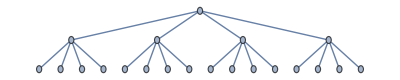

```mathematica
CompleteKaryTree[3, 4]
```

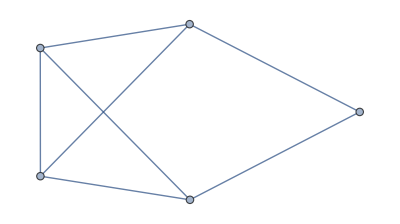

SparseArray[…]

```mathematica
x=RandomGraph[{5,7}]
AdjacencyMatrix[x]
```

```mathematica
MatrixForm[%27]
```

(0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
0 | 1 | 1 | 1 | 0)

```mathematica
MatrixForm[%25]
```

(1)
 |  |  |  |

```mathematica
MatrixForm[%19]
```

(1 | 1 | 1
1 | 1 | 1
1 | 1 | 1)

```mathematica
x=RandomGraph[5,7]
```

RandomGraph::dist: A graph distribution is expected at position 1 in RandomGraph[5,7].

RandomGraph[5,7]

```mathematica
AdjacencyMatrix[x]
```

AdjacencyMatrix::graph: A graph object is expected at position 1 in AdjacencyMatrix[RandomGraph[5,7]].

AdjacencyMatrix[RandomGraph[5,7]]

(0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 0 | 1
0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 0 | 1
1 | 1 | 0 | 1 | 0)

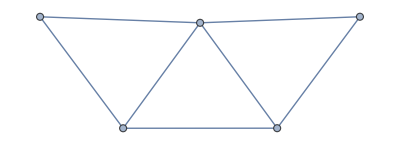

SparseArray[…]

```mathematica
MatrixForm[%50]
```

```mathematica
SocialMediaData["Facebook", "FriendNetwork"]
```

-Graphics-

```mathematica
Graph[Flatten[Table[i->j, {i,4}, {j,4}]]]
```

-Graphics-

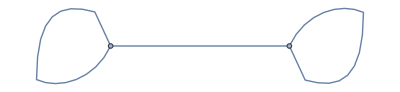
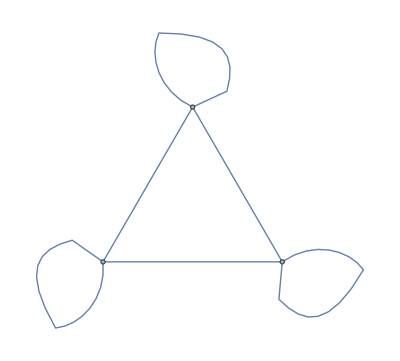
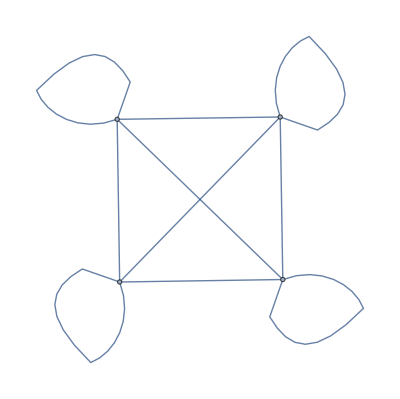
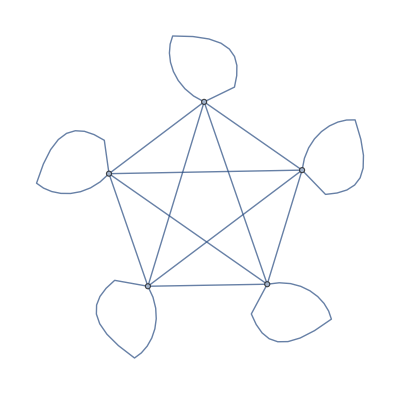
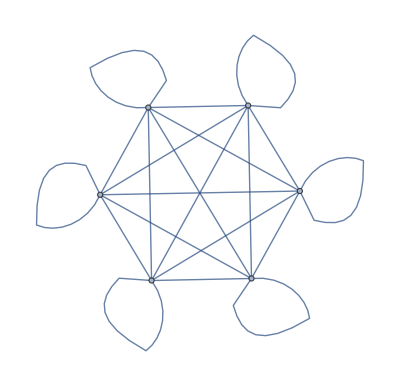
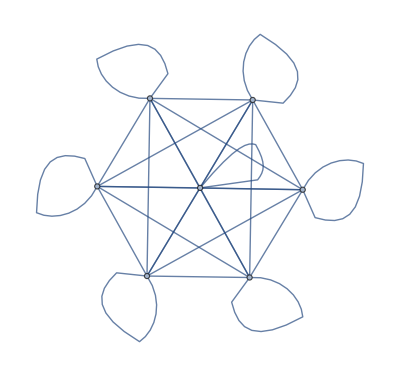
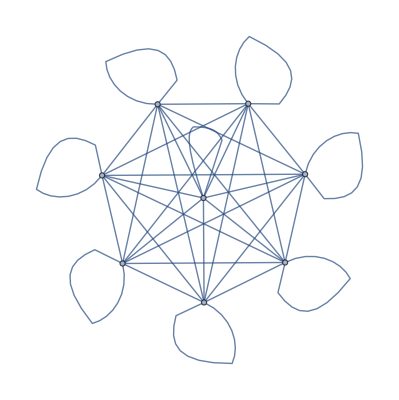
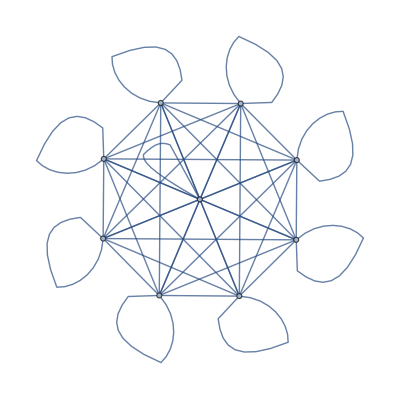

```mathematica
Table[UndirectedGraph[Flatten[Table[i -> j, {i, n}, {j, n}]]], {n, 2,10}]
```

```mathematica
Count[StringPart[WordList[], -1], "z"]
```

35

```mathematica
Reverse @ WordList[]
```

{zymurgy,zygotic,zygote,zydeco,zwieback,zucchini,zounds,zoophyte,zoom,zoology,zoologist,zoological,zoo,zoning,40099,abashed,abash,abasement,abase,abandonment,abandoned,abandon,abalone,abaft,abacus,aback,aardvark,aah,a}
 |  |  |  |

$OutputSizeLimit::nosess: This output can only be updated in the same kernel session that generated it.

```mathematica
Select[StringReverse[WordList[]]]
```

Select[{a,haa,kravdraa,kcaba,sucaba,tfaba,enolaba,nodnaba,denodnaba,tnemnodnaba,esaba,tnemesaba,hsaba,dehsaba,40099,gninoz,ooz,lacigolooz,tsigolooz,ygolooz,mooz,etyhpooz,sdnuoz,inihccuz,kcabeiwz,ocedyz,etogyz,citogyz,ygrumyz}]
 |  |  |  |

```mathematica
Prefix[List[5,4,6,7]]
```

Prefix[{5,4,6,7}]

```mathematica
l={4,5,6,67}
```

{4,5,6,67}

```mathematica
Prefix[Reverse[l]]
```

Prefix[{67,6,5,4}]

```mathematica
l // Reverse
```

{67,6,5,4}

```mathematica
Select[{1,2,3,4}, EvenQ]
```

{2,4}

```mathematica
Map[ToUpperCase, WordList[]]
```

{A,AAH,AARDVARK,ABACK,ABACUS,ABAFT,ABALONE,ABANDON,ABANDONED,ABANDONMENT,ABASE,ABASEMENT,ABASH,ABASHED,40099,ZONING,ZOO,ZOOLOGICAL,ZOOLOGIST,ZOOLOGY,ZOOM,ZOOPHYTE,ZOUNDS,ZUCCHINI,ZWIEBACK,ZYDECO,ZYGOTE,ZYGOTIC,ZYMURGY}
 |  |  |  |

```mathematica
StringTake[WordList[],1]
```

{a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a,40059,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z,z}
 |  |  |  |

```mathematica
Select[WordList[], StringTake[WordList[], 1]=='q']
```

Syntax::sntxf: "StringTake[WordList[],1]==" cannot be followed by "'q'".

```mathematica
Table[i->j, {i,2}, {j,2}] // Flatten
```

{1→1,1→2,2→1,2→2}

```mathematica
Flatten[Table[{1,2}, 3]]
```

{1,2,1,2,1,2}

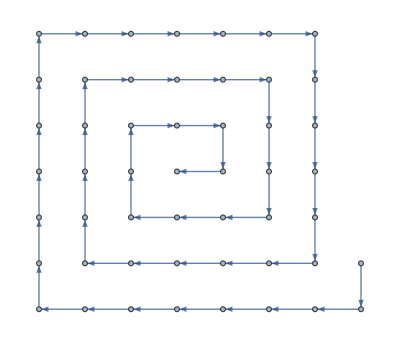

```mathematica
Table[i->i+1, {i, 50}] // Graph
```

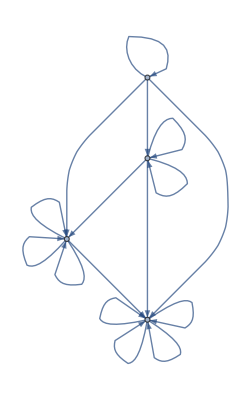

```mathematica
Flatten[Table[i->Max[i,j], {i,4}, {j,4}]] // Graph
```

```mathematica
Graph[Flatten[Table[i->Max[i,j], {i,4}, {j,4}]]] // AdjacencyMatrix // MatrixForm
```

(1 | 1 | 1 | 1
0 | 2 | 1 | 1
0 | 0 | 3 | 1
0 | 0 | 0 | 4)

```mathematica
MatrixForm[%6]
```

(1 | 1 | 1 | 1
0 | 2 | 1 | 1
0 | 0 | 3 | 1
0 | 0 | 0 | 4)

```mathematica
Table[i->j-i, {i,5}, {j,5}] // Flatten // Graph
```

-Graphics-

```mathematica
,m
```

```mathematica
data set
```

```mathematica
WordCounts["the fox jumped over the hare.", 2]
```

{the,hare}→1,{over,the}→1,{jumped,over}→1,{fox,jumped}→1,{the,fox}→1